# Method of particular solutions.

#### Fitting the sector eigenfunctions to a triangle.

{x→11.1287,c[1]→-0.0000178389}

19.8158

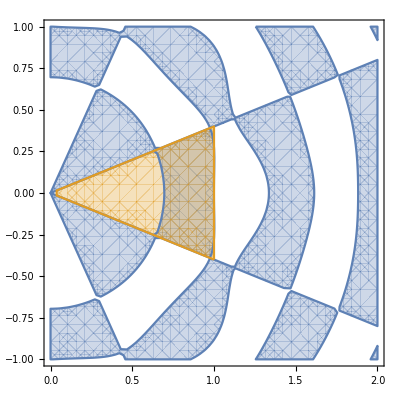

BesselJ[π/(2 ArcTan[2/5]),11.1287 r] Sin[(π (θ-ArcTan[2/5]))/(2 ArcTan[2/5])]-0.23963 BesselJ[(3 π)/(2 ArcTan[2/5]),11.1287 r] Sin[(3 π (θ-ArcTan[2/5]))/(2 ArcTan[2/5])]

0.

```mathematica
l=5/2;
M=1;
K=M;
q=π/(2ArcTan[1/l]);
u[r_,θ_]:=Table[10^(q i-q)BesselJ[q (2i-1),x r]Sin[q (2i -1)(θ-π/q/2)],{i,1,K+1}];
α[i_]=(i+0.4) π/q/2/(M+1);
mat=Table[u[1/Cos[α[i]],α[i]],{i,0,M}];
u0=Map[#==0&,mat.Table[c[i],{i,0,K}]];
c[0]=1;
Sequence@@Table[{c[i],RandomReal[]/10},{i,1,K}];
rt=FindRoot[u0,{x,BesselJZero[q,2]},Evaluate[%]]
approx=x^2/(l)^2/.%
u[r,θ].Table[c[i],{i,0,K}]/.rt;
%/.r->Sqrt[x^2+y^2]/.θ->ArcTan[y/x];
RegionPlot[{%>0,Sqrt[x^2+y^2]Cos[ArcTan[y/x]]≤1&&-π/q/2<ArcTan[y/x]<π/q/2},{x,0,2},{y,-1,1}]
fun=u[r,θ].Table[c[i],{i,0,K}]/.rt
%/.θ->π/q/2//Simplify
```

We just need to rationalize the numerical values in the above function to get a symbolic eigenfunction approximation.

#### Finding approximation error and bounds for the true eigenvalue of the triangle.

BesselJ[π/(2 ArcTan[2/5]),(345 r)/31] Sin[(π (θ-ArcTan[2/5]))/(2 ArcTan[2/5])]-6/25 BesselJ[(3 π)/(2 ArcTan[2/5]),(345 r)/31] Sin[(3 π (θ-ArcTan[2/5]))/(2 ArcTan[2/5])]

-BesselJ[π/(2 ArcTan[2/5]),(138 r)/31] Cos[(π θ)/(2 ArcTan[2/5])]-6/25 BesselJ[(3 π)/(2 ArcTan[2/5]),(138 r)/31] Cos[(3 π θ)/(2 ArcTan[2/5])]

-BesselJ[π/(2 ArcTan[2/5]),(345 Sec[θ])/31] Cos[(π θ)/(2 ArcTan[2/5])]-6/25 BesselJ[(3 π)/(2 ArcTan[2/5]),(345 Sec[θ])/31] Cos[(3 π θ)/(2 ArcTan[2/5])]

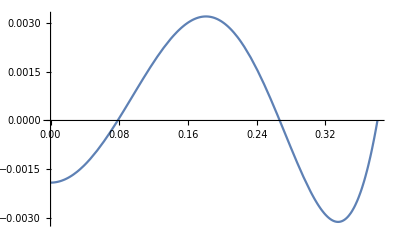

0.00319679

0.253096

0.019971

{19.4278,20.2196}

```mathematica
funr=fun/.rt//Rationalize[#,0.001]&
fun2=funr/.r->r/l//Simplify
funθ=%/.r->l/Cos[θ]
Plot[%,{θ,0,π/q/2}]
NMaximize[{Abs[%%],0≤θ≤π/q/2},θ,Method->"RandomSearch"][[1]]
NIntegrate[fun2^2r,{θ,-π/q/2,π/q/2},{r,0,l}]^(1/2)
Sqrt[l]%%/%
{approx/(1+%),approx/(1-%)}
```

The last pair of numbers gives bounds the true eigenvalue. Note that we are using only 2 eigenfunctions of the sector.